The present document is intended to explore the difference between the mean-field version of the Simple Trip model, one which includes the steady-state Time at Risk matrix and does not separate out the residents and visitors, and the Simple Trip model which explicitly includes movement of residents and visitors in and out of different compartments. 

We show here for the SIS model that there is no substantive difference between the equilibrium prevalence of the two versions of the Simple Trip model agree closely. (ie, in the plots below, the trends lie on top of one another.) We show that the agreement holds for eight different parameter regimes.

```mathematica
(* The TaR movement model *)
movtar ={0 == - ϕ1 n11 + τ12 n12,
0 == - ϕ2 n22+ τ21  n21,
(* Normalize to the residence populations *)
n11 + n12 == n1,
n22 + n21 == n2
};
(* The transmission model *)
sistar ={(* On-diagonal terms *)
0 == β1(i11 + i21)/(n11+n21)(n11 - i11) - γ i11 - ϕ1 i11 + τ12 i12,
0 == β2(i22 + i12)/(n22 + n12)(n22 - i22) - γ i22 - ϕ2 i22 + τ21 i21,
(* Off-diagonal terms *)
0 == β2(i22 + i12)/(n22 + n12)(n12 - i12) - γ i12 + ϕ1 i11 - τ12 i12,
0 == β1 (i11 + i21)/(n11 + n21)(n21 - i21) - γ i21 + ϕ2 i22 - τ21 i21
};
```

```mathematica
(* The Flux movement model *)
movflux ={0 == - f1 n1 + f2 n2,
(* Normalize to the total population *)
n ==n1+n2
};
(* The transmission model *)
sisflux ={
0 == β1  i1/n1(n1 - i1) - γ i1 - f1 i1 + f2 i2,
0 == β2  i2/n2(n2 - i2) - γ i2 -f2 i2+ f1 i1
};
```

```mathematica
(* Matching Flux Volumes *)
mtar ={m12-> (τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2,m21->(τ12 ϕ1)/(τ12+ϕ1)n1+(τ21 ϕ2)/(τ21+ϕ2)n2};
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar
```

{f1→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n1,f2→((n1 τ12 ϕ1)/(τ12+ϕ1)+(n2 τ21 ϕ2)/(τ21+ϕ2))/n2}

```mathematica
(* And the last step: using Dave's mean field version of the TaR model *)
movTarSols =Flatten[Solve[movtar,{n11,n12,n22,n21}]]
tarPsi = {{n11/n1, n12/n1},{n21/n2,n22/n2}}/.movTarSols
tarTarPsiEqs = tarPsi.{β1 i1/n1,β2 i2/n2}*{(n1-i1),(n2-i2)} -γ {i1,i2}
tarTarPsiEqs={0== -i1 γ+(-i1+n1) ((i1 β1 τ12)/(n1 (τ12+ϕ1))+(i2 β2 ϕ1)/(n2 (τ12+ϕ1))),0== -i2 γ+(-i2+n2) ((i2 β2 τ21)/(n2 (τ21+ϕ2))+(i1 β1 ϕ2)/(n1 (τ21+ϕ2)))}
```

{n11→(n1 τ12)/(τ12+ϕ1),n12→(n1 ϕ1)/(τ12+ϕ1),n22→(n2 τ21)/(τ21+ϕ2),n21→(n2 ϕ2)/(τ21+ϕ2)}

{{τ12/(τ12+ϕ1),ϕ1/(τ12+ϕ1)},{ϕ2/(τ21+ϕ2),τ21/(τ21+ϕ2)}}

{-i1 γ+(-i1+n1) ((i1 β1 τ12)/(n1 (τ12+ϕ1))+(i2 β2 ϕ1)/(n2 (τ12+ϕ1))),-i2 γ+(-i2+n2) ((i2 β2 τ21)/(n2 (τ21+ϕ2))+(i1 β1 ϕ2)/(n1 (τ21+ϕ2)))}

{0==-i1 γ+(-i1+n1) ((i1 β1 τ12)/(n1 (τ12+ϕ1))+(i2 β2 ϕ1)/(n2 (τ12+ϕ1))),0==-i2 γ+(-i2+n2) ((i2 β2 τ21)/(n2 (τ21+ϕ2))+(i1 β1 ϕ2)/(n1 (τ21+ϕ2)))}

## First : symmetric travel

```mathematica
tarpars= {ϕ1->.5/100, τ12 ->40/1,ϕ2->.5/100,τ21 ->40/1};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

## β = 2.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->2.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

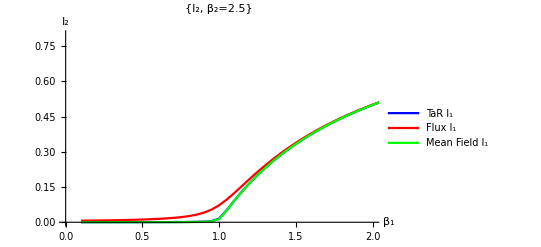

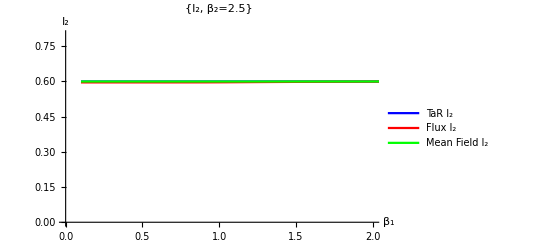

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## β = 0.5

```mathematica
sistar
```

{0==((i11+i21) (-i11+n11) β1)/(n11+n21)-i11 γ+i12 τ12-i11 ϕ1,0==((i12+i22) (-i22+n22) β2)/(n12+n22)-i22 γ+i21 τ21-i22 ϕ2,0==((i12+i22) (-i12+n12) β2)/(n12+n22)-i12 γ-i12 τ12+i11 ϕ1,0==((i11+i21) (-i21+n21) β1)/(n11+n21)-i21 γ-i21 τ21+i22 ϕ2}

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.movTarSols/.poppars/.tarpars/.sispars/.{β1->i,β2->0.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->0.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->0.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

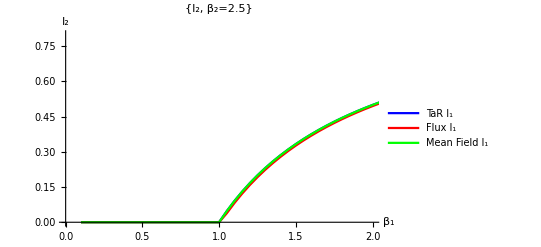

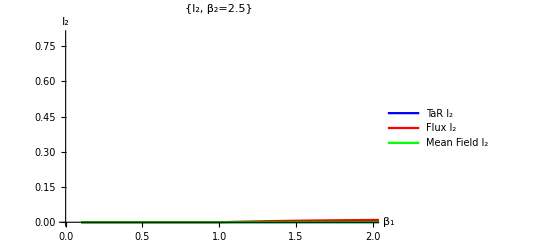

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## Second : Asymmetric travel

```mathematica
tarpars= {ϕ1->.5/10000, τ12 ->40/1,ϕ2->.5/100,τ21 ->40/1};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

## β = 2.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->2.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

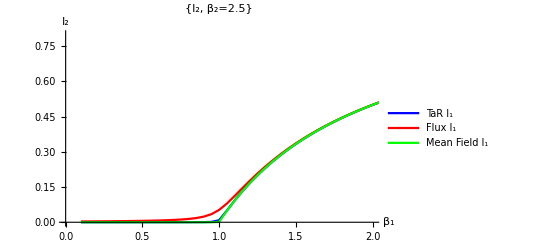

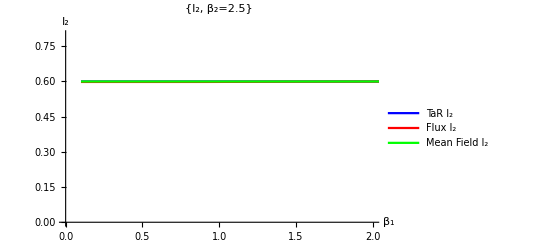

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## β = 0.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.movTarSols/.poppars/.tarpars/.sispars/.{β1->i,β2->0.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->0.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->0.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

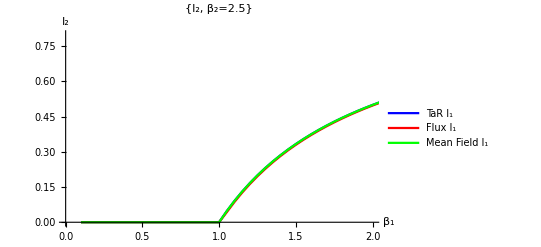

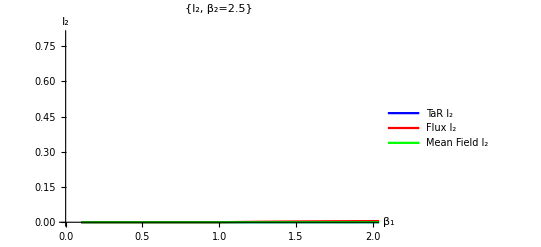

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## Third : symmetric travel, slow

```mathematica
tarpars= {ϕ1->.5/10000, τ12 ->40/100,ϕ2->.5/10000,τ21 ->40/100};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

## β = 2.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->2.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

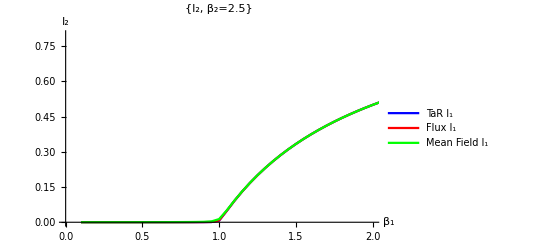

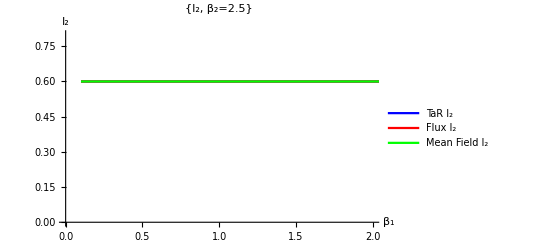

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## β = 0.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.movTarSols/.poppars/.tarpars/.sispars/.{β1->i,β2->0.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->0.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->0.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

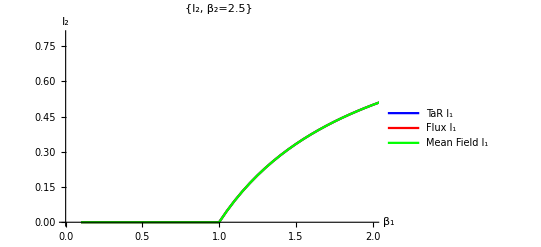

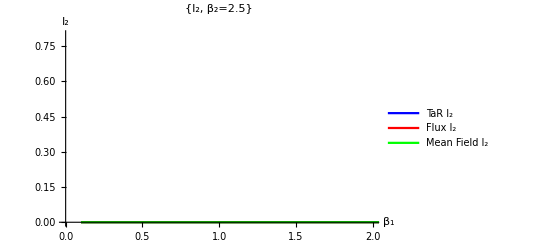

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## Fourth : Asymmetric travel, slow

```mathematica
tarpars=tarpars= {ϕ1->.5/1000000, τ12 ->40/100,ϕ2->.5/10000,τ21 ->40/100};
poppars={n1->500.,n2->500.};
sispars={γ->1.};
movTarSols =Flatten[NSolve[movtar/.tarpars/.poppars/.tarpars,{n11,n12,n22,n21}]];
fluxpars ={f1->(m12/n1),f2->(m21/n2)}/.mtar/.tarpars/.poppars;
movFluxSols= Flatten[Solve[movflux/.fluxpars/.n->1000,{n1,n2}]];
```

## β = 2.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.tarpars/.sispars/.movTarSols/.{β1->i,β2->2.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->2.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->2.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

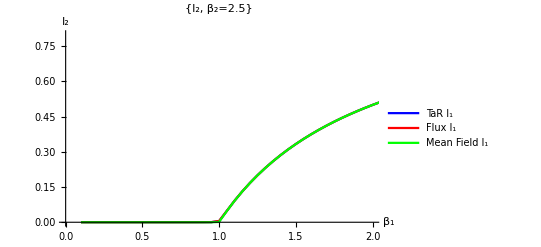

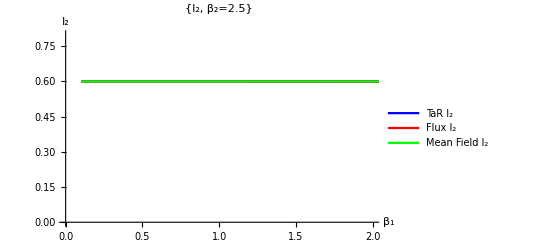

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```

## β = 0.5

```mathematica
tarPRSlices =Table[{i,(i11+i12)/n1/.poppars,(i22+i21)/n2/.poppars}/.FindRoot[sistar/.movTarSols/.poppars/.tarpars/.sispars/.{β1->i,β2->0.5},{i11,n1/2/.poppars,0,n1/.poppars},{i12,n1/2/.poppars,0,n1/.poppars},{i22,n2/2/.poppars,0,n2/.poppars},{i21,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fluxPRSlices =Table[{i,i1/n1/.poppars,i2/n2/.poppars}/.FindRoot[sisflux/.fluxpars/.sispars/.movFluxSols/.{β1->i,β2->0.5},{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

```mathematica
tarMFSlices = 
Table[{i, i1/n1/.poppars, i2/n2/.poppars}/.FindRoot[tarTarPsiEqs/.tarpars/.sispars/.movTarSols/.poppars/.{β1->i,β2->0.5},
{i1,n1/2/.poppars,0,n1/.poppars},{i2,n2/2/.poppars,0,n2/.poppars}],{i,.1,3,.05}];
```

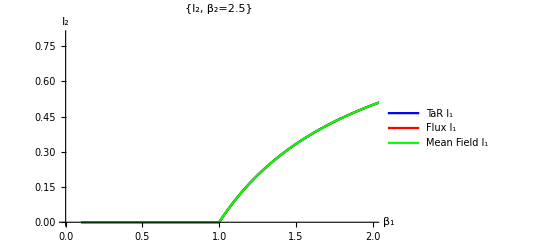

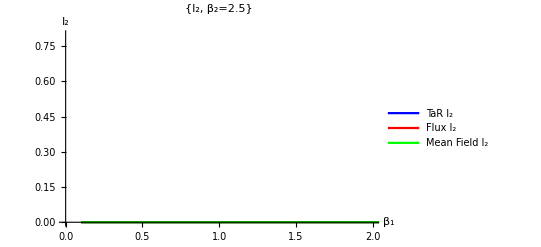

```mathematica
ListLinePlot[{tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],tarMFSlices[[;;,{1,2}]]
(*,tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]]*)},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{"TaR I_1","Flux I_1","Mean Field I_1"(*"TaR I_2","Flux I_2"*)},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]

ListLinePlot[{(*tarPRSlices[[;;,{1,2}]],fluxPRSlices[[;;,{1,2}]],*)
tarPRSlices[[;;,{1,3}]],fluxPRSlices[[;;,{1,3}]],tarMFSlices[[;;,{1,3}]]},PlotStyle->{Blue,Red, Green,Black},
PlotLegends->{(*"TaR I_1","Flux I_1",*)"TaR I_2","Flux I_2","Mean Field I_2"},
AxesLabel->{"β_1","I_2"},
PlotLabel->{"I_2, β_2=2.5"},
PlotRange->{{0,2},{0,.8}}]
```